# Double pendulum solutions

## Programming techniques

### Solving equation of motion

#### Typed from student sheet

```mathematica
m1=1.5;L1=1.2;g=9.81;
eq1={ theta1''[t]==-g/L1 Sin[theta1[t]]};
init={theta1[0]==2,theta1'[0]==0};
s1=NDSolve[{eq1,init},theta1,{t,0,10}][[1]];
```

#### Answers to questions

-Graphics-

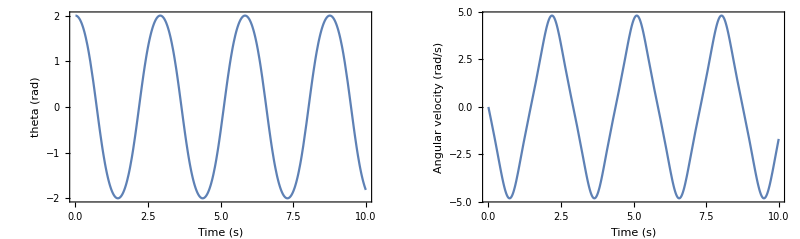

```mathematica
GraphicsGrid[{{
Plot[theta1[t]/.s1,{t,0,10},Frame->True,FrameLabel->{"Time (s)","theta (rad)"}],
(* Notice that the plot for theta1'[t] has moved away from a nice SHM sine wave. This is because we are allowing large angle variation and have the Sin[theta1[t]] in the equation of motion rather than the small angle approximation. *)
Plot[theta1'[t]/.s1,{t,0,10},Frame->True,FrameLabel->{"Time (s)","Angular velocity (rad/s)"}]}},ImageSize->Full]
```

-Graphics-

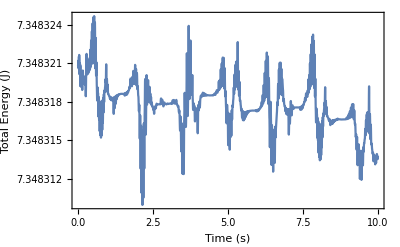

```mathematica
Plot[1/2 m1 L1^2 theta1'[t]^2- m1 g L1 Cos[theta1[t]]/.s1,{t,0,10},Frame->True,FrameLabel->{"Time (s)","Total Energy (J)"}]
```

At first glance, it may appear that the total energy is not conserved. However, on examining the values on the energy axis, you will see this variation is tiny. This is a result of both the way computers represent floating point numbers, and the finite step size in NDSolve. Solving with a prescribed, smaller MaxStepSize will allow the variation to be reduced, but will invariably take longer. If You set the PlotRange from 0-10 you will see a nice constant line.

### Animation

#### Typed from student sheet

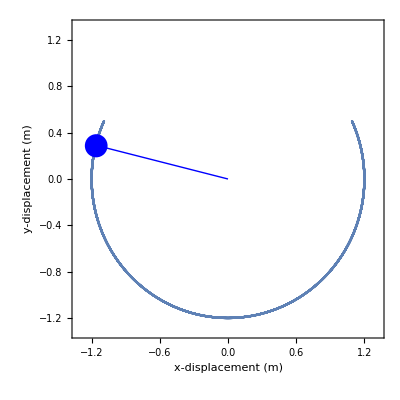

```mathematica
r1[t_]:=L1{ Sin[theta1[t]],- Cos[theta1[t]]}/.s1
path[tm_]:=ParametricPlot[r1[t],{t,0,tm},Epilog->{Blue,Disk[r1[tm],0.1],Line[{{0,0},r1[tm]}]},PlotRange->1.1 {{-L1,L1},{-L1,L1}},PlotPoints->60, 
Frame->True, FrameLabel->{"x-displacement (m)","y-displacement (m)"}]
path[10]
```

#### Answers to questions

-Graphics-

```mathematica
Animate[path[t],{t,0.01,10},AnimationRate->.5,AnimationRunning->False]
```

You will get an ““Endpoints for t in {t,0,0} must have distinct machine-precision numerical values.” error if you start the animation from t=0s as the ParametricPlot function would then try plotting from zero to zero and complain that these values are not distinct.

### Phase space

#### Typed from student sheet

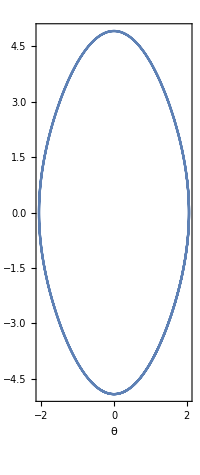

```mathematica
m1=1.5;L1=1.2;g=9.81;
sol=NDSolve[{eq1,theta1[0]==2,theta1'[0]==1},theta1,{t,0,10}][[1]];
ParametricPlot[{Mod[theta1[t]+π, 2 π] -π,theta1'[t]}/.sol,{t,0,10},Frame->True,FrameLabel->{"θ","θ'","Phase space"}]
```

#### Answers to questions

-Graphics-

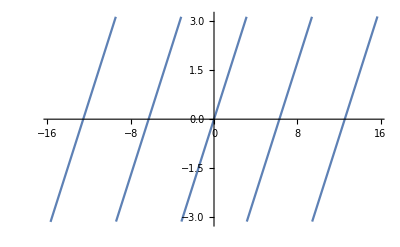

```mathematica
Plot[Mod[x+π,2π]-π,{x,-5π,5π}]
```

This a wrapping function. It takes any value of θ and wraps it back into the -π to π range.

-Graphics-

```mathematica
m1=1.5;L1=1.2;g=9.81;
Manipulate[
solm=NDSolve[{eq1,theta1[0]==th0,theta1'[0]==1},theta1,{t,0,10}][[1]];
ParametricPlot[{Mod[theta1[t]+π, 2 π]-π,theta1'[t]}/.solm,{t,0,10},Frame->True,PlotRange->{{-π,π},{-7,7}}],{{th0,0},-π,π}]
```

### Poincare maps

#### Typed from student sheet

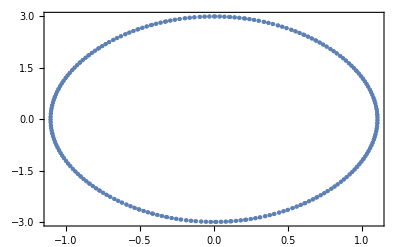

```mathematica
m1=1.5;L1=1.2;g=9.81;tmax=1000;
sol=NDSolve[{eq1,theta1[0]==0,theta1'[0]==3},theta1,{t,0,tmax}][[1]];
pt=Table[{Mod[theta1[t]+π, 2 π]-π,theta1'[t]}/.sol,{t,0,tmax,2 π Sqrt[L1/g]}];
ListPlot[pt,Frame->True]
```

#### Answers to questions

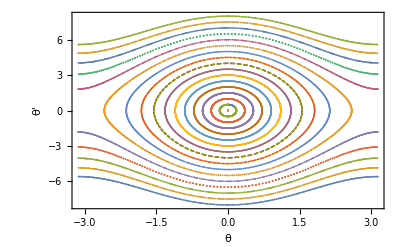

```mathematica
pts=Table[m1=1.5;L1=1.2;g=9.81;tmax=1000;
sol=NDSolve[{eq1,theta1[0]==0,theta1'[0]==w},theta1,{t,0,tmax}][[1]];
Table[{Mod[theta1[t]+π, 2 π]-π,theta1'[t]}/.sol,{t,0,tmax,2 π Sqrt[L1/g]}],{w,-8,8,0.5}];

ListPlot[pts,Frame->True,FrameLabel->{"θ","θ'","Poincare map"}]
```

## Study: Double pendulum

### Initial solution

-Graphics-

```mathematica
m1=1.3;
m2=1.3;
L1=1.2;
L2=1.2;
g=9.81;
tmax=10;

eq3={(m1+m2) L1 theta1''[t]+m2 L2 theta2''[t] Cos[theta1[t]-theta2[t]]+m2 L2 theta2'[t]^2 Sin[theta1[t]-theta2[t]]+g(m1+m2)Sin[theta1[t]]==0,m2 L2 theta2''[t]+m2 L1 theta1''[t]Cos[theta1[t]-theta2[t]]-m2 L1 theta1'[t]^2 Sin[theta1[t]-theta2[t]]+m2 g Sin[theta2[t]]==0};
init={theta1[0]==1,theta2[0]==0,theta1'[0]==0,theta2'[0]==0};

sol=NDSolve[{eq3,init},{theta1,theta2},{t,0,tmax}][[1]];
```

-Graphics-

### Animate path

```mathematica
(*set up functions for the position of the two pendulums *)
pos1[t_]:=L1{ Sin[theta1[t]],- Cos[theta1[t]]}/.sol;
pos2[t_]:=pos1[t]+L2{ Sin[theta2[t]],-Cos[theta2[t]]}/.sol;
```

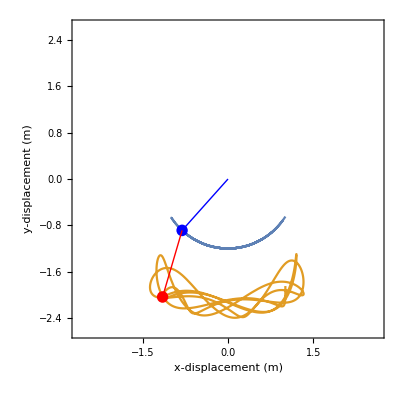

```mathematica
path2[tm_]:=ParametricPlot[{pos1[t],pos2[t]},{t,0,tm},Epilog->{Blue,Disk[pos1[tm],0.1],Line[{{0,0},pos1[tm]}],Red,Disk[pos2[tm],0.1],Line[{pos1[tm],pos2[tm]}]},PlotRange->{1.1{-L1-L2,L1+L2},1.1{-L1-L2,L1+L2}},PlotPoints->60,
Frame->True, FrameLabel->{"x-displacement (m)","y-displacement (m)"}]
path2[tmax] (* check that the function works for one value *)
Animate[path2[t],{t,1,tmax},AnimationRate->.5] (* animate through time range *)
```

-Graphics-

### Plot energies of system to check conservation

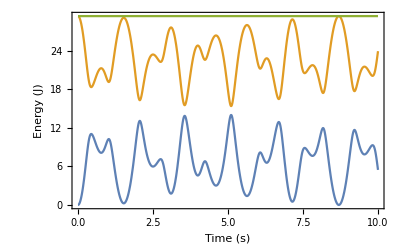

-Graphics-

```mathematica
(* here we don't force evaluate of the functions for plotting, so for each chosen time the delayed-assignment position functions need to be re-evaluated. This is useful if we were modifying some dependancies, but as we are not doing so here it just adds considerable time.*)
Plot[{1/2 m1 pos1'[t].pos1'[t]+1/2 m2 pos2'[t].pos2'[t],m1 g (L1+L2+pos1[t][[2]])+m2 g (L1+L2+pos2[t][[2]]),1/2 m1 pos1'[t].pos1'[t]+1/2 m2 pos2'[t].pos2'[t]+m1 {0,g}.pos1[t]+m2 {0,g}.pos2[t]+m1 g (L1+L2)+m2 g (L1+L2)},{t,0,tmax},PlotRange->All,Frame->True, FrameLabel->{"Time (s)", "Energy (J)"}]

(* here we force evaluation of the functions for plotting, this then sets the first argument of Plot for all values of time, meaning evaluation is done quickly for each chosen time value *)
Plot[{1/2 m1 pos1'[t].pos1'[t]+1/2 m2 pos2'[t].pos2'[t],m1 g (L1+L2+pos1[t][[2]])+m2 g (L1+L2+pos2[t][[2]]),1/2 m1 pos1'[t].pos1'[t]+1/2 m2 pos2'[t].pos2'[t]+m1 {0,g}.pos1[t]+m2 {0,g}.pos2[t]+m1 g (L1+L2)+m2 g (L1+L2)}//Evaluate,{t,0,tmax},
PlotRange->All,Frame->True, FrameLabel->{"Time (s)", "Energy (J)"}]

(* you might be interested to try postfixing these two Plot functions with the Timing function to see the advantage of forcing evaluation *)
```

-Graphics-

### Solve again for 1000 seconds and create phase space and Poincare map

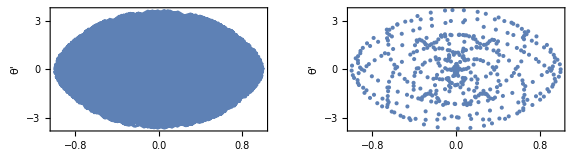

```mathematica
m1=1.3;
m2=1.3;
L1=1.2;
L2=1.2;
g=9.81;
tmax=1000;

eq3={(m1+m2) L1 theta1''[t]+m2 L2 theta2''[t] Cos[theta1[t]-theta2[t]]+m2 L2 theta2'[t]^2 Sin[theta1[t]-theta2[t]]+g(m1+m2)Sin[theta1[t]]==0,m2 L2 theta2''[t]+m2 L1 theta1''[t]Cos[theta1[t]-theta2[t]]-m2 L1 theta1'[t]^2 Sin[theta1[t]-theta2[t]]+m2 g Sin[theta2[t]]==0};

init={theta1[0]==1,theta2[0]==0,theta1'[0]==0,theta2'[0]==0};

sol=NDSolve[{eq3,init},{theta1,theta2},{t,0,tmax}][[1]];

(* The motion is sampled at regular intervals. In this case at the period of the upper pendulum. *)
pm1=Table[{Mod[theta1[t]+π, 2 π]-π,theta1'[t]}/.sol//Evaluate,{t,0,tmax,2π Sqrt[ L1/g]}];

GraphicsGrid[{{ParametricPlot[{Mod[theta1[t]+π, 2 π] -π,theta1'[t]}/.sol,{t,0,tmax},Frame->True,FrameLabel->{"θ","θ'","Phase space"},AspectRatio->0.5],
ListPlot[{pm1},Frame->True,FrameLabel->{"θ","θ'","Poincare map"}]}},ImageSize->Large]
```

### Modified Poincare map trigger

14.0701

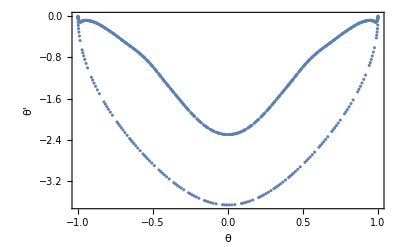

```mathematica
m1=1.3;
m2=1.3;
L1=1.2;
L2=1.2;
g=9.81;
tmax=1000;
eq3={(m1+m2) L1 theta1''[t]+m2 L2 theta2''[t] Cos[theta1[t]-theta2[t]]+m2 L2 theta2'[t]^2 Sin[theta1[t]-theta2[t]]+g(m1+m2)Sin[theta1[t]]==0,m2 L2 theta2''[t]+m2 L1 theta1''[t]Cos[theta1[t]-theta2[t]]-m2 L1 theta1'[t]^2 Sin[theta1[t]-theta2[t]]+m2 g Sin[theta2[t]]==0};

init={theta1[0]==1,theta2[0]==0,theta1'[0]==0,theta2'[0]==0};

pm2={}; (* start with an empty list for our special points *)

(*The Event condition limits the dimensionality of the problem - theta2 contrained. We will also set the total energy which further contrains the problem *) sol=NDSolve[{eq3,init,WhenEvent[theta2[t]==0&&theta2'[t]>0,AppendTo[pm2,{theta1[t],theta1'[t]}]]},{theta1,theta2},{t,0,tmax}][[1]];

pos1[t_]:=L1{ Sin[theta1[t]],- Cos[theta1[t]]}/.sol;
pos2[t_]:=pos1[t]+L2{ Sin[theta2[t]],-Cos[theta2[t]]}/.sol;

(* calculate the total energy of the system *)
1/2 m1 pos1'[0].pos1'[0]+1/2 m2 pos2'[0].pos2'[0]+m1 {0,g}.pos1[0]+m2 {0,g}.pos2[0]+m1 g L1+m2 g (L1+L2)

ListPlot[pm2,Frame->True,FrameLabel->{"θ","θ'","Poincare map"}]
```

-Graphics-

### Deduce initial angular velocity given a total energy

This step is done analytically and we need to clear all value first.

```mathematica
g=. ;L1=.;L2=.;m1=.;m2=.;Et=.
θ1=.;θ2=.;ω1=.;ω2=.;

r1[t_]=L1{ Sin[theta1[t]],- Cos[theta1[t]]};
r2[t_]=r1[t]+L2{ Sin[theta2[t]],-Cos[theta2[t]]};

ene=1/2 m1 r1'[t].r1'[t]+1/2 m2 r2'[t].r2'[t]+m1 g (r1[t][[2]]+L1+L2)+m2 g (r2[t][[2]]+L1+L2);

eq=(Et==ene/.{theta1[t]->θ1,theta2[t]->θ2,theta1'[t]->ω1,theta2'[t]->ω2});

(* Given θ1, θ2, ω1 and total energy, get expression for ω2 *)
sw2=Solve[eq,ω2][[1]]//FullSimplify
```

{ω2→1/(2 L2 √m2)(-2 L1 √m2 ω1 Cos[θ1-θ2]-√(8 Et-8 g (L1+L2) (m1+m2)-2 L1^2 (2 m1+m2) ω1^2+2 L1 (4 g (m1+m2) Cos[θ1]+L1 m2 ω1^2 Cos[2 (θ1-θ2)])+8 g L2 m2 Cos[θ2]))}

-Graphics-

### Compose multiple Poincare maps for energy 30 J

```mathematica
(* It is a good idea to initally limit the size of the dataset being calculated. Limit the ω2 range and the time interval to make sure the method is working before doing the whole dataset. *)
```

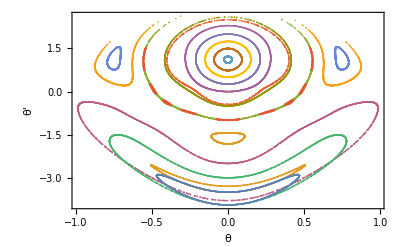

```mathematica
m1=1.3;
m2=1.3;
L1=1.2;
L2=1.2;

g=9.81;
tmax=3000;

(* Because we are defining specific energy values, it is important that the definition of the zero for potential energy is as detailed in the conservation of energy question, i.e. θ1=θ2=0 *)
Et=30;

tr30=Table[
θ1=0;
ω1=w;
θ2=0;
If[Im[ω2/.sw2]==0,
eq3={(m1+m2) L1 theta1''[t]+m2 L2 theta2''[t] Cos[theta1[t]-theta2[t]]+m2 L2 theta2'[t]^2 Sin[theta1[t]-theta2[t]]+g(m1+m2)Sin[theta1[t]]==0,m2 L2 theta2''[t]+m2 L1 theta1''[t]Cos[theta1[t]-theta2[t]]-m2 L1 theta1'[t]^2 Sin[theta1[t]-theta2[t]]+m2 g Sin[theta2[t]]==0};
init={theta1[0]==θ1,theta2[0]==θ2,theta1'[0]==ω1,theta2'[0]==ω2/.sw2};
pm2={};
NDSolve[{eq3,init,WhenEvent[theta2[t]==0&&theta2'[t]>0,AppendTo[pm2,{theta1[t],theta1'[t]}]]},{theta1,theta2},{t,0,tmax}][[1]];
pm2,{{0,0}}],{w,-4,4,.5}];

ListPlot[tr30,Frame->True,FrameLabel->{"θ","θ'","Poincare map"},PlotRange->All]
```

-Graphics-

### Redo for total energy of 35 J

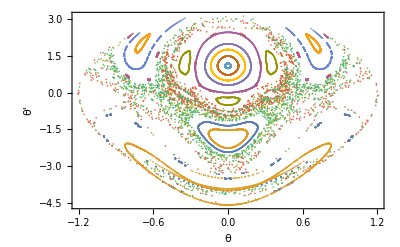

```mathematica
m1=1.3;
m2=1.3;
L1=1.2;
L2=1.2;

g=9.81;
tmax=3000;
Et=35;

tr35=Table[
θ1=0;
ω1=w;
θ2=0;
If[Im[ω2/.sw2]==0,
eq3={(m1+m2) L1 theta1''[t]+m2 L2 theta2''[t] Cos[theta1[t]-theta2[t]]+m2 L2 theta2'[t]^2 Sin[theta1[t]-theta2[t]]+g(m1+m2)Sin[theta1[t]]==0,m2 L2 theta2''[t]+m2 L1 theta1''[t]Cos[theta1[t]-theta2[t]]-m2 L1 theta1'[t]^2 Sin[theta1[t]-theta2[t]]+m2 g Sin[theta2[t]]==0};
init={theta1[0]==θ1,theta2[0]==θ2,theta1'[0]==ω1,theta2'[0]==ω2/.sw2};
pm2={};
NDSolve[{eq3,init,WhenEvent[theta2[t]==0&&theta2'[t]>0,AppendTo[pm2,{theta1[t],theta1'[t]}]]},{theta1,theta2},{t,0,tmax}][[1]];
pm2,{{0,0}}],{w,-4,4,.5}];

ListPlot[tr35,Frame->True,FrameLabel->{"θ","θ'","Poincare map"},PlotRange->All]
```